# qLanth : Optical Transitions

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"];
Get["misc.m"];
```

## The Magnetic Dipole Operator

```mathematica
TabulateManyJJBlockMagDipTables[{1,2,3,4,5,6,7},"Overwrite"->True]
```

<|1→/Users/juan/ZiaLab/Codebase/qlanth/hams/f1_JJBlockMatrixTable-magDip.m,2→/Users/juan/ZiaLab/Codebase/qlanth/hams/f2_JJBlockMatrixTable-magDip.m,3→/Users/juan/ZiaLab/Codebase/qlanth/hams/f3_JJBlockMatrixTable-magDip.m,4→/Users/juan/ZiaLab/Codebase/qlanth/hams/f4_JJBlockMatrixTable-magDip.m,5→/Users/juan/ZiaLab/Codebase/qlanth/hams/f5_JJBlockMatrixTable-magDip.m,6→/Users/juan/ZiaLab/Codebase/qlanth/hams/f6_JJBlockMatrixTable-magDip.m,7→/Users/juan/ZiaLab/Codebase/qlanth/hams/f7_JJBlockMatrixTable-magDip.m|>

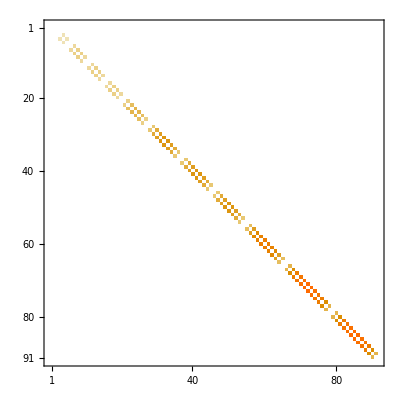

-Graphics-

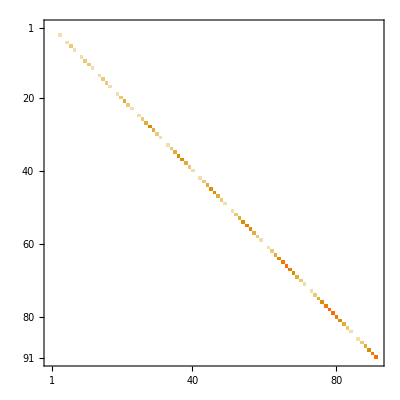

```mathematica
numE=2;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->1}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
MatrixPlot[Abs[magx]]
MatrixPlot[Abs[magy]]
MatrixPlot[Abs[magz]]
```

### Tests

```mathematica
numE=2;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->1}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
MatrixPlot[Abs[magx]]
MatrixPlot[Abs[magy]]
MatrixPlot[Abs[magz]]
```

-Graphics-

-Graphics-

-Graphics-

Commutators

```mathematica
Commutator[op1_,op2_]:=op1.op2-op2.op1;
permutations=Permutations[{1,2,3}];
Table[
(
{idx1,idx2,idx3}=permutation;
sign=Signature[permutation];
Max@Flatten[Abs[Commutator[magOp[[idx1]],magOp[[idx2]]]-I sign*magOp[[idx3]]]]
)
,{permutation,permutations}]
```

{0,0,0,0,0,0}

Manual check on numE=2

```mathematica
TFun=Transpose;
idx=3;
prettybasis[[idx]]
{a,b}={1,1};
Print["jx : ",Simplify[a(prettybasis).TFun[magx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[magy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[magz][[idx]]]]
idx=idx+1;
prettybasis[[idx]]
Print["jx : ",Simplify[a(prettybasis).TFun[magx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[magy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[magz][[idx]]]]
idx=idx+1;
prettybasis[[idx]]
Print["jx : ",Simplify[a(prettybasis).TFun[magx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[magy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[magz][[idx]]]]
```

3P{1,-1}

jx : (3P{1,0})/(√2)

jy : -(ⅈ (3P{1,0}))/(√2)

jz : -(3P{1,-1})

3P{1,0}

jx : (3P{1,-1}+3P{1,1})/(√2)

jy : (ⅈ (3P{1,-1}-3P{1,1}))/(√2)

jz : 0

3P{1,1}

jx : (3P{1,0})/(√2)

jy : (ⅈ (3P{1,0}))/(√2)

jz : 3P{1,1}

Putting gs=1 should lead to matrix spectrum of J

```mathematica
Off[Eigenvalues::arh];
numE=7;
eigenTruth={"J^2s",N[(#*(#+1))]&/@AllowedJ[numE]}
{"MJs",N[Sort[DeleteDuplicates[Flatten[AllowedMforJ/@AllowedJ[numE]]]]]}
magOp=ReplaceInSparseArray[#,{gs->1}]&/@MagDipoleMatrixAssembly[numE];
{Jx,Jy,Jz}=magOp;
Jsquared=Simplify[ Jx.Jx+ Jy.Jy+Jz.Jz];
{"J^2s*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jsquared]]//Chop,0.001]]}
{"MJxs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jx]]//Chop,0.001]]}
{"MJys*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jy]]//Chop,0.001]]}
{"MJzs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jz]]//Chop,0.001]]}
```

{J^2s,{0.75,3.75,8.75,15.75,24.75,35.75,48.75,63.75,80.75,99.75,120.75,143.75,168.75}}

{MJs,{-12.5,-11.5,-10.5,-9.5,-8.5,-7.5,-6.5,-5.5,-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5}}

{J^2s*,{0.75,3.75,8.75,15.75,24.75,35.75,48.75,63.75,80.75,99.75,120.75,143.75,168.75}}

{MJxs*,{-12.5,-11.5,-10.5,-9.5,-8.5,-7.5,-6.5,-5.5,-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5}}

{MJys*,{-12.5,-11.5,-10.5,-9.5,-8.5,-7.5,-6.5,-5.5,-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5}}

{MJzs*,{-12.5,-11.5,-10.5,-9.5,-8.5,-7.5,-6.5,-5.5,-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5}}

Putting gs=0 should lead to matrix spectrum of L

```mathematica
Off[Eigenvalues::arh];
numE=7;
allowedL=DeleteDuplicates[Sort[Last/@FindSL/@First/@AllowedNKSLJTerms[numE]]];
eigenTruth={"L^2s",N[(#*(#+1))]&/@allowedL}
{"MLs",N[DeleteDuplicates[Sort[Flatten[Range[-#,#]&/@allowedL]]]]}
magOp=ReplaceInSparseArray[#,{gs->0}]&/@MagDipoleMatrixAssembly[numE];
{Lx,Ly,Lz}=magOp;
Lsquared=Simplify[ Lx.Lx+ Ly.Ly+Lz.Lz];
{"L^2s*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lsquared]]//Chop,0.001]]}
{"MLxs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lx]]//Chop,0.001]]}
{"MLys*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Ly]]//Chop,0.001]]}
{"MLzs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lz]]//Chop,0.001]]}
```

{L^2s,{0.,2.,6.,12.,20.,30.,42.,56.,72.,90.,110.,132.,156.}}

{MLs,{-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.}}

{L^2s*,{0.,2.,6.,12.,20.,30.,42.,56.,72.,90.,110.,132.,156.}}

{MLxs*,{-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.}}

{MLys*,{-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.}}

{MLzs*,{-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.}}

Putting gs = very-large should lead to matrix spectrum of S, sort of

```mathematica
Off[Eigenvalues::arh];
numE=3;
η=10^10;
allowedS=DeleteDuplicates[Sort[First/@FindSL/@First/@AllowedNKSLJTerms[numE]]];
eigenTruth={"S^2s",N[(#*(#+1))]&/@allowedS}
{"MSs",N[DeleteDuplicates[Sort[Flatten[Range[-#,#]&/@allowedS]]]]}
magOp=ReplaceInSparseArray[#,{gs->η}]&/@MagDipoleMatrixAssembly[numE];
{Sx,Sy,Sz}=magOp;
Ssquared=Simplify[ Sx.Sx+ Sy.Sy+Sz.Sz];
{"S^2s*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Ssquared]]//Chop,0.001]]}
{"MSxs*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sx]]//Chop,0.001]]}
{"MSys*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sy]]//Chop,0.001]]}
{"MSzs*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sz]]//Chop,0.001]]}
```

{S^2s,{0.75,3.75}}

{MSs,{-1.5,-0.5,0.5,1.5}}

{S^2s*,{7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,7.5×10^9,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10,3.75×10^10}}

{MSxs*,{-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5}}

{MSys*,{-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5}}

{MSzs*,{-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5}}

## Pr in LaF3

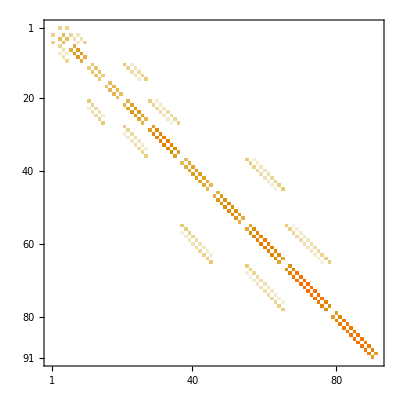

-Graphics-

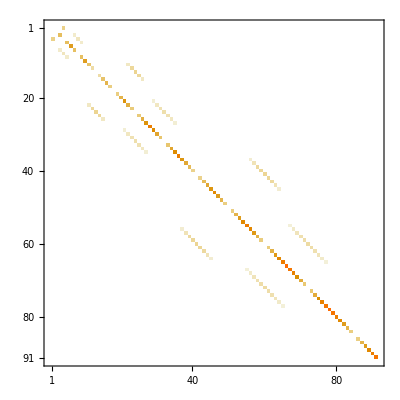

```mathematica
numE=2;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->2}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
MatrixPlot[Abs[magx]]
MatrixPlot[Abs[magy]]
MatrixPlot[Abs[magz]]
```

```mathematica
{rmsDifference,carnallEnergies,eigenEnergies,ln,
carnallAssignments,simplerStateLabels,eigensys,basis,truncatedStates}=Import["./calcs/Pr in LaF3 - example.m"];
```

```mathematica
(*the eigenvectors as columns*)
allEigen=Transpose[Last/@eigensys];
```

```mathematica
Sx=ConjugateTranspose[allEigen].magx.allEigen;
Sy=ConjugateTranspose[allEigen].magy.allEigen;
Sz=ConjugateTranspose[allEigen].magz.allEigen;
Stot=Abs[Sx]^2+Abs[Sy]^2+Abs[Sz]^2;
```

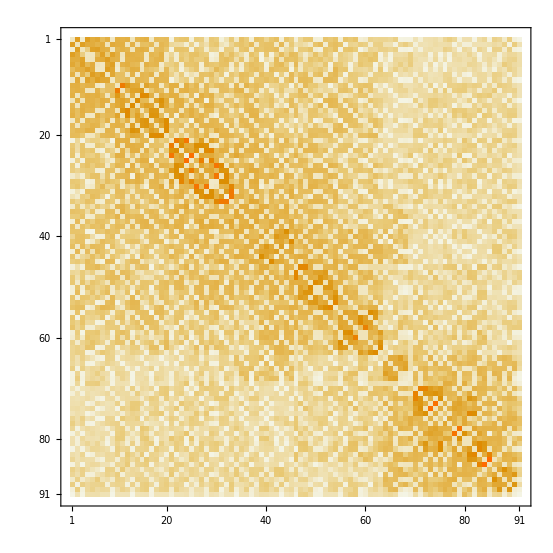

```mathematica
MatrixPlot[Stot]
```

```mathematica
μ0=4π×10^-7;
h=6.626*10^-34;
μB=9.274×10^-24;
me=9.109×10^-31;
c=2.998*10^8;
e=1.602*10^-19;

{minλ,maxλ}={300,10000};
minfMD=0.015;
maxLen=20;

{Sx,Sy,Sz}=ConjugateTranspose[allEigen].#.allEigen&/@{magx,magy,magz};
SMDALL=μB^2*(Abs[Sx]^2+Abs[Sy]^2+Abs[Sz]^2);
SMDGS=SMDALL[[;;,1]];
(*calculate transition wavelenghts from excited to ground states*)
energyDifferences=Outer[Subtract,eigenEnergies,eigenEnergies];
transitionWaveLengthsInMeters=1/energyDifferences/100;
transitionWaveLengthsInNanoMeters=10^9*transitionWaveLengthsInMeters;
groundStateEnergyDifferences=energyDifferences[[;;,1]];
groundStateTransitionWavelenghtsInMeters=transitionWaveLengthsInMeters[[;;,1]];
groundStateTransitionWavelenghtsInNanometers=groundStateTransitionWavelenghtsInMeters*10^9;
fMD=(8 π^2 me)/(3 h e^2 c)(1/groundStateTransitionWavelenghtsInMeters) ;
fMD=fMD*SMDGS;
AMD=16 π^3 μ0/(3 h)*(1/transitionWaveLengthsInMeters^3)*SMDALL;
lifetimes=1/AMD;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
lowToHigh=Reverse[Ordering[fMD]];
tabular=Transpose[{Last/@truncatedStates,
Round[#,1]&/@groundStateTransitionWavelenghtsInNanometers,
Round[#,1]&/@eigenEnergies,
ScientificForm[#,2]&/@(fMD*10^8)}];
tabular=tabular[[lowToHigh]];
tabular=Select[tabular,And[minλ<=#[[2]]<=maxλ,ToExpression[ToString[#[[-2]]]]>=minfMD]&];
tabular=tabular[[;;Min[Length[tabular],maxLen]]];
Grid[Prepend[tabular,{"ψ2","λ/nm","ΔE/cm^-1","fMD X 10^8"}],Frame->All]
```

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

ψ2 | λ/nm | ΔE/cm^-1 | fMD X 10^8
-0.42 3H{5,-5}-0.53 3H{5,-1}-0.53 3H{5,1}-0.19 3H{5,3}-0.42 3H{5,5} | 4566 | 2190 | 4.2
-0.25 3H{5,-4}-0.89 3H{5,0}+0.2 3H{5,2}-0.25 3H{5,4} | 4703 | 2126 | 3.9
-0.62 3H{5,-5}-0.19 3H{5,-3}-0.27 3H{5,-1}+0.27 3H{5,1}+0.19 3H{5,3}+0.62 3H{5,5} | 4315 | 2317 | 3.7
0.31 3H{5,-3}-0.61 3H{5,-1}+0.61 3H{5,1}-0.31 3H{5,3}-0.17 3H{5,5} | 4635 | 2158 | 2.
0.29 3H{5,-4}+0.63 3H{5,-2}+0.12 3H{5,0}+0.63 3H{5,2}+0.29 3H{5,4} | 4358 | 2295 | 1.7
-0.24 3H{5,-5}-0.53 3H{5,-3}+0.39 3H{5,-1}+0.39 3H{5,1}-0.53 3H{5,3}-0.24 3H{5,5} | 4368 | 2289 | 6.7×10^-1
-0.21 3F{3,-3}+0.66 3F{3,-1}+0.66 3F{3,1}-0.21 3F{3,3} | 1520 | 6579 | 2.4×10^-1
-0.29 3H{5,-5}+0.6 3H{5,-3}+0.23 3H{5,-1}-0.23 3H{5,1}-0.6 3H{5,3}+0.29 3H{5,5} | 3938 | 2540 | 1.9×10^-1
-0.08 3F{2,1}+0.5 3H{5,-5}-0.41 3H{5,-3}-0.25 3H{5,-1}-0.25 3H{5,1}-0.41 3H{5,3}+0.5 3H{5,5} | 4146 | 2412 | 1.7×10^-1
0.65 3F{2,-1}-0.65 3F{2,1}+0.14 3H{6,-5}+0.17 3H{6,-3}-0.17 3H{6,3}-0.14 3H{6,5} | 1896 | 5275 | 1.5×10^-1
0.32 1G{4,-3}+0.46 1G{4,-1}+0.46 1G{4,1}+0.32 1G{4,3}+0.24 3F{4,-3}+0.35 3F{4,-1}+0.35 3F{4,1}+0.24 3F{4,3} | 1007 | 9927 | 1.4×10^-1
0.59 3H{5,-4}-0.22 3H{5,-2}-0.42 3H{5,0}-0.22 3H{5,2}+0.59 3H{5,4} | 4103 | 2437 | 1.4×10^-1
-0.29 1G{4,-3}+0.21 1G{4,-1}+0.21 1G{4,1}-0.29 1G{4,3}+0.49 3F{4,-3}-0.34 3F{4,-1}-0.34 3F{4,1}+0.49 3F{4,3} | 1398 | 7152 | 1.3×10^-1
-0.68 3F{2,-2}+0.68 3F{2,2}+0.12 3H{6,2} | 1930 | 5182 | 1.2×10^-1
-0.52 1G{4,-1}+0.52 1G{4,1}+0.12 1G{4,3}-0.44 3F{4,-1}+0.44 3F{4,1} | 1024 | 9762 | 1.2×10^-1
0.68 3F{3,-3}-0.68 3F{3,3}+0.08 3F{4,3} | 1549 | 6456 | 9.5×10^-2
0.41 1G{4,-3}-0.41 1G{4,3}-0.57 3F{4,-3}+0.57 3F{4,3}+0.09 3H{4,3} | 1422 | 7034 | 7.9×10^-2
-0.66 3F{3,-3}-0.22 3F{3,-1}-0.22 3F{3,1}-0.66 3F{3,3} | 1509 | 6628 | 7.7×10^-2
0.25 3H{6,-3}-0.65 3H{6,-1}+0.65 3H{6,1}-0.25 3H{6,3} | 2315 | 4321 | 6.6×10^-2
-0.69 3F{3,-1}+0.69 3F{3,1}+0.1 3H{6,5} | 1537 | 6507 | 6.×10^-2

-Graphics-

```mathematica
truncatedStates=ParseStatesByNumBasisVecs[eigensys,basis,4,0.001,"Coefficients"->"Probabilities"];
simpleFromTo=Outer[#1->#2&,simplerStateLabels,simplerStateLabels];
fromTo=Outer[{#1,#2}&,Last/@truncatedStates,Last/@truncatedStates];
indexPairs=Outer[{#1,#2}&,Range[Length[eigensys]],Range[Length[eigensys]]];
energyPairs=Outer[{#1,#2}&,eigenEnergies,eigenEnergies];
```

```mathematica
PrettySaundersSLJmJ[{"1S",0,0}]
```

1S{0,0}

```mathematica
truncatedStates[[1]]
```

{0,2. % 1G{4,0}+9.6 % 3H{4,-4}+77.7 % 3H{4,0}+9.6 % 3H{4,4}}

```mathematica
header={"ψ_i->ψ_f","ψ_i","ψ_f",Tooltip["A_MD/s^-1","Spontaneous Decay Rate"],Tooltip["τ/s","Radiative Lifetime"],Tooltip["λ/nm","Emission Wavelength"],"i","j","Ei/cm^-1","Ef/cm^-1"};
{minλ,maxλ}={300,1700};
takeOnly=20;
allTransitions={simpleFromTo,
fromTo,
AMD,
lifetimes,
transitionWaveLengthsInNanoMeters,
indexPairs,
energyPairs};
allTransitions=(Flatten/@Transpose[Flatten[#,1]&/@allTransitions]);

allTransitions=Select[allTransitions,And[#[[4]]>0,minλ<=#[[6]]<=maxλ]&];
allTransitions=SortBy[allTransitions,#[[5]]&];
Grid[Prepend[allTransitions[[;;takeOnly]],header],Frame->All]
```

ψ_i->ψ_f | ψ_i | ψ_f | A_MD/s^-1 | τ/s | λ/nm | i | j | Ei/cm^-1 | Ef/cm^-1
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 9.9 % 1I{6,-1}+9.9 % 1I{6,1}+36.9 % 3P{1,-1}+36.9 % 3P{1,1} | 5.53886 | 0.180543 | 394.095 | 91 | 80 | 46964.7 | 21590.2
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.2 % 1I{6,-3}+0.2 % 1I{6,3}+49.4 % 3P{1,-1}+49.4 % 3P{1,1} | 3.32608 | 0.300654 | 392.969 | 91 | 77 | 46964.7 | 21517.4
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.3 % 1I{6,-2}+0.3 % 1I{6,2}+0.1 % 1I{6,4}+99. % 3P{1,0} | 3.13244 | 0.31924 | 392.474 | 91 | 76 | 46964.7 | 21485.3
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 2.65496 | 0.376654 | 398.789 | 91 | 84 | 46964.7 | 21888.8
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 1.15869 | 0.863044 | 397.442 | 91 | 83 | 46964.7 | 21803.9
1D2→3F2 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 46.5 % 3F{2,-2}+46.5 % 3F{2,2}+1.5 % 3H{6,-2}+1.5 % 3H{6,2} | 0.741892 | 1.34791 | 837.912 | 67 | 35 | 17116.9 | 5182.5
1I6→1G4 | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 16.5 % 1G{4,-4}+21.4 % 1G{4,0}+16.5 % 1G{4,4}+12.4 % 3F{4,0} | 0.526187 | 1.90046 | 844.101 | 83 | 59 | 21803.9 | 9956.93
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 37.9 % 1I{6,-3}+10.6 % 1I{6,-1}+10.6 % 1I{6,1}+37.9 % 1I{6,3} | 0.517487 | 1.93242 | 391.014 | 91 | 73 | 46964.7 | 21390.2
1I6→1G4 | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 6.6 % 1G{4,-4}+41.4 % 1G{4,0}+6.6 % 1G{4,4}+21.7 % 3F{4,0} | 0.515803 | 1.93873 | 840.823 | 84 | 60 | 21888.8 | 9995.72
3F4→3H4 | 24.4 % 3F{4,-3}+11.8 % 3F{4,-1}+11.8 % 3F{4,1}+24.4 % 3F{4,3} | 1.3 % 1G{4,-2}+1.3 % 1G{4,2}+46.2 % 3H{4,-2}+46.2 % 3H{4,2} | 0.509121 | 1.96417 | 1466.6 | 54 | 7 | 7152.02 | 333.517
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 1.2 % 1D{2,-1}+1.2 % 1D{2,1}+47.8 % 3F{2,-1}+47.8 % 3F{2,1} | 0.492871 | 2.02893 | 834.384 | 68 | 36 | 17169.7 | 5184.8
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 42.3 % 3F{2,-1}+42.3 % 3F{2,1}+3.1 % 3H{6,-3}+3.1 % 3H{6,3} | 0.425296 | 2.3513 | 840.743 | 68 | 38 | 17169.7 | 5275.44
1D2→3F2 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 9.1 % 3F{2,-2}+66.5 % 3F{2,0}+9.1 % 3F{2,2}+3.3 % 3H{6,6} | 0.395407 | 2.52904 | 846.533 | 66 | 37 | 17082.4 | 5269.51
1D2→3F3 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 44.1 % 3F{3,-3}+4.7 % 3F{3,-1}+4.7 % 3F{3,1}+44.1 % 3F{3,3} | 0.383216 | 2.6095 | 953.405 | 67 | 44 | 17116.9 | 6628.2
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 1.1 % 3F{3,-3}+47. % 3F{3,-1}+47. % 3F{3,1}+1.1 % 3F{3,3} | 0.371738 | 2.69007 | 945.624 | 66 | 41 | 17082.4 | 6507.37
1D2→3F3 | 44.6 % 1D{2,-1}+44.6 % 1D{2,1}+4. % 3P{2,-1}+4. % 3P{2,1} | 31.6 % 3F{3,-2}+31.5 % 3F{3,0}+31.6 % 3F{3,2}+1.3 % 3F{4,4} | 0.369631 | 2.7054 | 961.093 | 65 | 40 | 16894.8 | 6489.97
1I6→1G4 | 13.7 % 1I{6,-6}+56.6 % 1I{6,0}+4. % 1I{6,2}+13.7 % 1I{6,6} | 24.6 % 1G{4,-3}+11.4 % 1G{4,-1}+11.4 % 1G{4,1}+24.6 % 1G{4,3} | 0.367658 | 2.71992 | 896.828 | 82 | 63 | 21666.3 | 10515.9
1I6→3H6 | 41. % 1I{6,-2}+14.5 % 1I{6,0}+41. % 1I{6,2}+0.8 % 3P{2,0} | 6.3 % 3H{6,-3}+42.7 % 3H{6,-1}+42.7 % 3H{6,1}+6.3 % 3H{6,3} | 0.366748 | 2.72667 | 579.119 | 79 | 24 | 21588.2 | 4320.64
1D2→3F3 | 44.5 % 1D{2,-2}+44.5 % 1D{2,2}+4.1 % 3P{2,-2}+4.1 % 3P{2,2} | 46.3 % 3F{3,-3}+1.1 % 3F{3,-1}+1.1 % 3F{3,1}+46.3 % 3F{3,3} | 0.366241 | 2.73044 | 958.706 | 64 | 39 | 16887.1 | 6456.39
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 15. % 3F{3,-2}+64.3 % 3F{3,0}+15. % 3F{3,2}+1. % 3H{6,4} | 0.358472 | 2.78962 | 966.918 | 66 | 45 | 17082.4 | 6740.26

```mathematica
{123,123,123,123}*100"%"
```

{12300 %,12300 %,12300 %,12300 %}